The model of Stover et al. on incorporating demographic heterogeneity. In this model, there are two phenotypes that can potentially differ in birth rates and death rates. It is possible for one phenotype to give birth to individuals of the other phenotype.

```mathematica
dn1=(β11 n1+β21 n2) (1-n1-n2)-δ1 n1;
dn2=(β12 n1+β22 n2) (1-n1-n2)-δ2 n2;
```

The mortality heterogeneity model is the following:

```mathematica
dn1=β/2(n1+n2)(1-n1-n2)-δ1 n1;
dn2=β/2(n1+n2) (1-n1-n2)-δ2 n2;
```

If there was no heterogeneity, the equilibrium would be the following:

```mathematica
Simplify[Solve[β n1 (1-n1)-δ1 n1==0,n1]]
```

{{n1→0},{n1→1-δ1/β}}

With heterogeneity, then, the equilibrium is the following:

```mathematica
equil=Solve[{dn1==0,dn2==0},{n1,n2}]
Simplify[equil[[2,1,2]]+equil[[2,2,2]]]
```

{{n1→0,n2→0},{n1→(δ2 (β δ1+β δ2-2 δ1 δ2))/(β (δ1+δ2)^2),n2→δ1^2/(δ1+δ2)^2+(δ1 δ2)/(δ1+δ2)^2-(2 δ1^2 δ2)/(β (δ1+δ2)^2)}}

1-(2 δ1 δ2)/(β (δ1+δ2))

The equilibrium with heterogeneity will be larger than the equilibrium without heterogeneity if phenotype 2 has a lower mortality rate than the first phenotype. That is, of course, super obvious.

```mathematica
Assuming[β>0&&δ1>0&&δ2>0,Simplify[1-(2 δ1 δ2)/(β (δ1+δ2))>1-δ1/β]]
```

δ1>δ2

A better comparison would be if there were three phenotypes, one of which had a higher mortality rate, and one of which had a lower mortality rate. Here let’s assume that n2 has the “mean” phenotype, and n1 has a lower mortality rate, and n3 has a higher mortality rate.

```mathematica
dn1=β/3(n1+n2+n3)(1-n1-n2-n3)-δ1 n1;
dn2=β/3(n1+n2+n3)(1-n1-n2-n3)-δ2 n2;
dn3=β/3(n1+n2+n3)(1-n1-n2-n3)-δ3 n3;
```

The equilibrium of this model is the following:

```mathematica
equil=Solve[{dn1==0,dn2==0,dn3==0},{n1,n2,n3}]
Simplify[equil[[2,1,2]]+equil[[2,2,2]]+equil[[2,3,2]]]
```

{{n1→0,n2→0,n3→0},{n1→(δ2 δ3 (β δ1 δ2+β δ1 δ3+β δ2 δ3-3 δ1 δ2 δ3))/(β (δ1 δ2+δ1 δ3+δ2 δ3)^2),n2→(δ1^2 δ2 δ3)/(δ1 δ2+δ1 δ3+δ2 δ3)^2+(δ1^2 δ3^2)/(δ1 δ2+δ1 δ3+δ2 δ3)^2+(δ1 δ2 δ3^2)/(δ1 δ2+δ1 δ3+δ2 δ3)^2-(3 δ1^2 δ2 δ3^2)/(β (δ1 δ2+δ1 δ3+δ2 δ3)^2),n3→(δ1^2 δ2^2)/(δ1 δ2+δ1 δ3+δ2 δ3)^2+(δ1^2 δ2 δ3)/(δ1 δ2+δ1 δ3+δ2 δ3)^2+(δ1 δ2^2 δ3)/(δ1 δ2+δ1 δ3+δ2 δ3)^2-(3 δ1^2 δ2^2 δ3)/(β (δ1 δ2+δ1 δ3+δ2 δ3)^2)}}

(β δ2 δ3-3 δ1 δ2 δ3+β δ1 (δ2+δ3))/(β (δ2 δ3+δ1 (δ2+δ3)))

The n2 equilibrium in a homogeneous population would be 1-δ_2/β.

The heterogeneous population will have a higher equilibrium if:

```mathematica
Assuming[β>0&&δ1>0&&δ2>0&&δ3>0,FullSimplify[(β δ2 δ3-3 δ1 δ2 δ3+β δ1 (δ2+δ3))/(β (δ2 δ3+δ1 (δ2+δ3)))>1-δ2/β]]
```

δ2 (δ1+δ3)>2 δ1 δ3

Let’s just assume, for simplicity’s sake, that n1’s mortality rate is x units smaller and n3’s mortality rate is x units larger. Then the heterogeneous population will have a higher carrying capacity if:

```mathematica
Assuming[δ2>0,Simplify[δ2 (δ1+δ3)>2 δ1 δ3/.{δ1->δ2-x,δ3->δ2+x}]]
```

x^2>0

In this model, heterogeneity of the additive variety will always increase the carrying capacity, assuming that heterogeneity is even between the two phenotypes. That’s interesting. What if the heterogeneity is not even? Here, n1 has a lower mortality rate (x units smaller) and n3 has a higher mortality rate (y units larger). Then the inequality is: 2 x y>δ_2 (y-x). If x > y, then this will always be satisfied (which makes sense, since the difference is biased towards n1).

```mathematica
Assuming[δ2>0,Simplify[δ2 (δ1+δ3)>2 δ1 δ3/.{δ1->δ2-x,δ3->δ2+y}]]
```

x (2 y+δ2)>y δ2

Even if y < x, it would still be possible for this inequality to be satisfied, and the heterogeneous population equilibrium to be larger. For example:

```mathematica
x (2 y+δ2)>y δ2/.{β->1,δ2->0.5,x->0.2,y->0.3}
```

True

What if the heterogeneity is not additive, but is rather multiplicative? In this case, n1 has its mortality rate reduced by a factor x, and n3 has its mortality increased by a factor y. In this case, heterogeneity will increase the carrying capacity if the following is true:

```mathematica
Assuming[δ2>0,Simplify[δ2 (δ1+δ3)>2 δ1 δ3/.{δ1->δ2 x,δ3->δ2 y}]]
```

x+y>2 x y

We can simplify this a bit further by solving the inequality for y:

```mathematica
x+y>2 x y;
y-2x y>-x;
y(1-2 x)>-x
(* If x < 1/2 then 1-2x > 0 and this can be rewritten as *)
y>-x/(1-2x)
(* this inequality will ALWAYS be true *)
```

If the first phenotype has a mortality rate that is less than half as much as the second phenotype, then the carrying capacity will always be increased.

```mathematica
y(1-2 x)>-x
(* If x > 1/2 then 1-2x < 0 and this can be rewritten as *)
y<-x/(1-2x)
```

It’s easiest to visualize this as a region in x-y space, since we know that y > 1 and x < 1. Basically, the upshot here is that, when x > 1/2, there will be y values (the shaded region below) where the carrying capacity is still increased by heterogeneity, but also a region where heterogeneity decreases the carrying capacity.

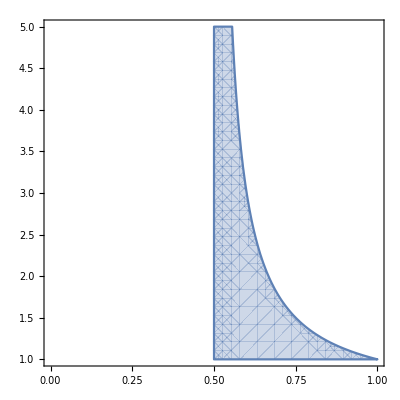

```mathematica
RegionPlot[y<-x/(1-2x),{x,0,1},{y,1,5}]
```

So heterogeneity will tend to increase the carrying capacity, unless the heterogeneity is biased towards a phenotype with a higher mortality rate. Of course, this was considering the case where every phenotype was equally likely to be produced by any other phenotype. In the GEM without evolution (where heritability is 0), there is actually a bias towards producing the intermediate phenotype. Just for giggles, let’s explore that model by assuming that the probability of producing n2 is higher than n1 or n3.

```mathematica
dn1=β/4(n1+n2+n3)(1-n1-n2-n3)-δ1 n1;
dn2=β/2(n1+n2+n3)(1-n1-n2-n3)-δ2 n2;
dn3=β/4(n1+n2+n3)(1-n1-n2-n3)-δ3 n3;
```

The equilibrium of this model is the following:

```mathematica
equil=Solve[{dn1==0,dn2==0,dn3==0},{n1,n2,n3}]
Simplify[equil[[2,1,2]]+equil[[2,2,2]]+equil[[2,3,2]]]
```

{{n1→0,n2→0,n3→0},{n1→(δ2 δ3 (β δ1 δ2+2 β δ1 δ3+β δ2 δ3-4 δ1 δ2 δ3))/(β (δ1 δ2+2 δ1 δ3+δ2 δ3)^2),n2→(2 δ1^2 δ2 δ3)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2+(4 δ1^2 δ3^2)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2+(2 δ1 δ2 δ3^2)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2-(8 δ1^2 δ2 δ3^2)/(β (δ1 δ2+2 δ1 δ3+δ2 δ3)^2),n3→(δ1^2 δ2^2)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2+(2 δ1^2 δ2 δ3)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2+(δ1 δ2^2 δ3)/(δ1 δ2+2 δ1 δ3+δ2 δ3)^2-(4 δ1^2 δ2^2 δ3)/(β (δ1 δ2+2 δ1 δ3+δ2 δ3)^2)}}

(β δ1 δ2+2 β δ1 δ3+β δ2 δ3-4 δ1 δ2 δ3)/(β δ1 δ2+2 β δ1 δ3+β δ2 δ3)

```mathematica
Assuming[β>0&&δ1>0&&δ2>0&&δ3>0,Simplify[(β δ1 δ2+2 β δ1 δ3+β δ2 δ3-4 δ1 δ2 δ3)/(β δ1 δ2+2 β δ1 δ3+β δ2 δ3)>1-δ2/β]]
```

δ2 (δ1+δ3)>2 δ1 δ3

This is the same as above, verifying the differences in heritability don’t affect the results.

The other thing that differs in our model is that, really, there are additive differences in b that translate into multiplicative differences in d. 

If the phenotypes are evenly distributed, then mortality heterogeneity still definitely increases the carrying capacity in a deterministic model.

```mathematica
Assuming[a>0&&x>0,Simplify[Expand[δ2 (δ1+δ3)>2 δ1 δ3/.{δ2->a b2^2,δ1->a (b2+x)^2, δ3->a (b2-x)^2} ]]]
```

3 b2^2>x^2

Let’s start with the simplest case of reproductive heterogeneity.

```mathematica
dn1=1/3(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n1;
dn2=1/3(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n2;
dn3=1/3(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n3;
```

The equilibrium of this model is the following:

```mathematica
equil=Solve[{dn1==0,dn2==0,dn3==0},{n1,n2,n3}]
Simplify[equil[[2,1,2]]+equil[[2,2,2]]+equil[[2,3,2]]]
```

{{n1→0,n2→0,n3→0},{n1→(β1+β2+β3-3 δ)/(3 (β1+β2+β3)),n2→(β1+β2+β3-3 δ)/(3 (β1+β2+β3)),n3→(β1+β2+β3-3 δ)/(3 (β1+β2+β3))}}

(β1+β2+β3-3 δ)/(β1+β2+β3)

For the carrying capacity to be increased, you need to satisfy the following inequality:

```mathematica
Assuming[δ>0&&β1>0&&β2>0&&β3>0,Simplify[(β1+β2+β3-3 δ)/(β1+β2+β3)>1-δ/β2]]
```

β1+β3>2 β2

Again, we can consider some different cases. If reproductive heterogeneity is additive and even between the two other phenotypes then heterogeneity has no effect on the carrying capacity, which is quite different from the case of mortality heterogeneity.

```mathematica
β1+β3>2 β2/.{β1->β2+x,β3->β2-x}
```

2 β2>2 β2

```mathematica
Simplify[(β1+β2+β3-3 δ)/(β1+β2+β3)/.{β1->β2+x,β3->β2-x}]
```

1-δ/β2

If the additive differences are not equal, then reproductive heterogeneity will increase the carrying capacity if n1 has its birth rate increased by more than the amount that n2 has its birth rate decreased.

```mathematica
Assuming[β2>0,Simplify[β1+β3>2 β2/.{β1->β2+x,β3->β2-y}]]
```

x>y

If the differences are multiplicative (with x > 1 and y < 1), then the carrying capacity will be increased whenever x + y > 2. So, if the differences are balanced (e.g. x = 1.1 and y = 0.9) then there will be no effect on the carrying capacity, as before. If n1 has more than double the birth rate of n2, then the carrying capacity will be increased regardless. Otherwise, the carrying capacity will be increased or decreased, depending on the bias.

```mathematica
Assuming[β2>0,Simplify[β1+β3>2 β2/.{β1->β2 x,β3->β2 y}]]
```

x+y>2

As before, changing the heritabilities doesn’t affect these results.

```mathematica
dn1=1/4(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n1;
dn2=1/2(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n2;
dn3=1/4(β1 n1+β2 n2+β3 n3)(1-n1-n2-n3)-δ n3;
equil=Solve[{dn1==0,dn2==0,dn3==0},{n1,n2,n3}]
Simplify[equil[[2,1,2]]+equil[[2,2,2]]+equil[[2,3,2]]]
Assuming[δ>0&&β1>0&&β2>0&&β3>0,Simplify[(β1+2 β2+β3-4 δ)/(β1+2 β2+β3)>1-δ/β2]]
```

Also, notice that I cannot work with a 3d version of our logistic model because it’s not really solvable analytically.

```mathematica
dn1=1/3(b-bs (n1+n2+n3)) (n1+n2+n3)-(d1+ds (n1+n2+n3)) n1
dn2=1/3(b-bs (n1+n2+n3)) (n1+n2+n3)-(d2+ds (n1+n2+n3)) n2
dn3=1/3(b-bs (n1+n2+n3)) (n1+n2+n3)-(d3+ds (n1+n2+n3)) n3
```

1/3 (n1+n2+n3) (b-bs (n1+n2+n3))-n1 (d1+ds (n1+n2+n3))

1/3 (n1+n2+n3) (b-bs (n1+n2+n3))-n2 (d2+ds (n1+n2+n3))

1/3 (n1+n2+n3) (b-bs (n1+n2+n3))-n3 (d3+ds (n1+n2+n3))

```mathematica
equil=Solve[{dn1==0,dn2==0,dn3==0},{n1,n2,n3}]
```

$Aborted